# Waveplates and polarization tomography

P. Huft

## definitions

```mathematica
QWP[θ_]:=({{1, ⅈ Sin[2θ]}, {ⅈ Sin[2θ], ⅇ^(ⅈ(2θ-π/2))}}); (*this is from Fowles*)(*θ is the angle of the fast axis in the lab, where 0 = vertical*)
QWP[0]//MatrixForm
QWP[π/2]//MatrixForm
QWP[π/4]//MatrixForm
QWP[0].{1,0}
QWP[π/2].{1,0}
QWP[π/4].{1,0}//FullSimplify
```

(1 | 0
0 | -ⅈ)

(1 | 0
0 | ⅈ)

(1 | ⅈ
ⅈ | 1)

{1,0}

{1,0}

{1,ⅈ}

```mathematica
HWP[θ_]:=({{Cos[2θ], Sin[2θ]}, {Sin[2θ], -Cos[2θ]}});(*θ is the angle of the fast axis in the lab, where 0 = vertical*)
HWP[0]//MatrixForm
HWP[π/2]//MatrixForm
HWP[π/4]//MatrixForm
HWP[0].{1,0}
HWP[π/2].{1,0}
HWP[π/4].{1,0}
```

(1 | 0
0 | -1)

(-1 | 0
0 | 1)

(0 | 1
1 | 0)

{1,0}

{-1,0}

{0,1}

```mathematica
HWP[θ].QWP[θ].{Cos[θ],Sin[θ]}//FullSimplify
```

{1/4 ⅇ^(-ⅈ θ) ((1+2 ⅈ)+2 Cos[2 θ]+(1-2 ⅈ) Cos[4 θ]+ⅈ Sin[4 θ]),1/4 (-Cos[3 θ]+Cos[5 θ]+(2+4 ⅈ) Sin[θ]+(2-ⅈ) Sin[3 θ]-ⅈ Sin[5 θ])}

## polarization state tomography

### single qubit (pure) state tomography - extract Stokes parameters

```mathematica
Clear[α,β,ϕ,γ];
χ={α,β ⅇ^(ⅈ ϕ)};
χstar={α,β ⅇ^(-ⅈ ϕ)};
ρ=KroneckerProduct[χ,χstar];
ρ//MatrixForm
σ0=({{1, 0}, {0, 1}});σ3=({{1, 0}, {0, -1}});σ2=({{0, -ⅈ}, {ⅈ, 0}});σ1=({{0, 1}, {1, 0}});
```

(α^2 | ⅇ^(-ⅈ ϕ) α β
ⅇ^(ⅈ ϕ) α β | β^2)

Reconstruct the state by expansion onto the Pauli matrices, where the coefficients are the Stokes parameters

```mathematica
-Graphics-;
```

```mathematica
"S0"
S0=Tr[σ0.ρ]
"S1"
S1=Tr[σ1.ρ]
"S2"
S2=Tr[σ2.ρ]
"S3"
S3=Tr[σ3.ρ]
1/2(S0 σ0+S1 σ1+S2 σ2+S3 σ3)//FullSimplify//MatrixForm
```

S0

α^2+β^2

S1

ⅇ^(-ⅈ ϕ) α β+ⅇ^(ⅈ ϕ) α β

S2

ⅈ ⅇ^(-ⅈ ϕ) α β-ⅈ ⅇ^(ⅈ ϕ) α β

S3

α^2-β^2

(α^2 | ⅇ^(-ⅈ ϕ) α β
ⅇ^(ⅈ ϕ) α β | β^2)

But what waveplate configurations do we need to do these measurements in the lab? Suppose I have a hwp, qwp, and linear polarizer in series. Can I do the same measurements?

Equivalent to measuring the Stokes parameters as shown above is measuring the overlap of the unknown state with V, D, and R, the results of which together fully quantify the state.

```mathematica
d=1/(√2){1,1};A=1/(√2){1,-1};
L=1/(√2){1,ⅈ};R=1/(√2){1,-ⅈ};
V={0,1};H={1,0};
"project on V"
Refine[Abs[V.χ]^2,Assumptions->ϕ∈Reals&&α∈Reals&&β∈Reals]
"project on D"
Refine[Abs[d.χ]^2,Assumptions->ϕ∈Reals&&α∈Reals&&β∈Reals]//TrigExpand
"project on R"
Refine[Abs[L.χ]^2,Assumptions->ϕ∈Reals&&α∈Reals&&β∈Reals]
```

project on V

β^2

project on D

Abs[α/(√2)+(ⅇ^(ⅈ ϕ) β)/(√2)]^2

project on R

Abs[α/(√2)+(ⅈ ⅇ^(ⅈ ϕ) β)/(√2)]^2

Matrix projectors for the six pairs of states (an over-complete set of measurements):

```mathematica
"V projector"
projV=KroneckerProduct[V,V];
projV//MatrixForm
"H projector"
projH=KroneckerProduct[H,H];
projH//MatrixForm
"A projector"
projA=KroneckerProduct[A,A];
projA//MatrixForm
"D projector"
projD=KroneckerProduct[d,d];
projD//MatrixForm
"L projector"
projL=KroneckerProduct[L,L];
projL//MatrixForm
"R projector"
projR=KroneckerProduct[R,R];
projR//MatrixForm
```

V projector

(0 | 0
0 | 1)

H projector

(1 | 0
0 | 0)

A projector

(1/2 | -1/2
-1/2 | 1/2)

D projector

(1/2 | 1/2
1/2 | 1/2)

L projector

(1/2 | ⅈ/2
ⅈ/2 | -1/2)

R projector

(1/2 | -ⅈ/2
-ⅈ/2 | -1/2)

Verify that the projectors act as expected:

```mathematica
Tr[projV.ρ]
Tr[projD.ρ]//ExpToTrig
Tr[projL.ρ]//ExpToTrig
```

β^2

α^2/2+β^2/2+α β Cos[ϕ]

α^2/2-β^2/2+ⅈ α β Cos[ϕ]

By inspection the V projector is just a linear polarizer oriented to transmit vertically polarized light, as expected. The others are not described by single elements. We want to be able to express each of these, up to an irrelevant overall phase, by a fixed linear polarizer preceded by a quarter and half waveplate which can have any angle wrt vertical

```mathematica
projV.QWP[0].HWP[0]
Tr[projV.QWP[0].HWP[0].ρ]
```

{{0,0},{0,ⅈ}}

ⅈ β^2

```mathematica
Tr[projV.QWP[0].HWP[π/4].ρ]
```

-ⅈ ⅇ^(-ⅈ ϕ) α β

```mathematica
Tr[projV.QWP[π/4].HWP[0].ρ]
```

ⅈ ⅇ^(-ⅈ ϕ) α β-β^2

```mathematica
Tr[projV.QWP[π/4].HWP[π/4].ρ]
```

ⅇ^(-ⅈ ϕ) α β+ⅈ β^2

```mathematica
projA
```

{{1/2,-1/2},{-1/2,1/2}}

```mathematica
HWP[θ].QWP[ϕ]
(*Tr[projV.QWP[0].HWP[0].ρ]*)
```

{{0,ⅇ^(ⅈ (-π/2+2 ϕ)) Sin[2 θ]+ⅈ Cos[2 θ] Sin[2 ϕ]},{0,-ⅇ^(ⅈ (-π/2+2 ϕ)) Cos[2 θ]+ⅈ Sin[2 θ] Sin[2 ϕ]}}

```mathematica
V
```

{0,1}

```mathematica
HWP[π/4].V
```

{1,0}

```mathematica
HWP[π/4].H
```

{0,1}

```mathematica
HWP[π/4].d
```

{1/(√2),1/(√2)}

```mathematica
HWP[π/4].A
```

{-1/(√2),1/(√2)}

ⅈ β^2

### single qubit (pure) state tomography - method 2:

```mathematica
Clear[α,β,ϕ,γ];
χ=({{α}, {β ⅇ^(ⅈ ϕ)}});
χstar={α,β ⅇ^(-ⅈ ϕ)};
ρ=KroneckerProduct[χ,χstar];
ρ//MatrixForm
V={0,1};
LP=({{0, 0}, {0, 1}});
(*linear polarizer with vertical transmission*)
σ0=({{1, 0}, {0, 1}});σ3=({{1, 0}, {0, -1}});σ2=({{0, -ⅈ}, {ⅈ, 0}});σ1=({{0, 1}, {1, 0}});
```

(α^2 | ⅇ^(-ⅈ ϕ) α β
ⅇ^(ⅈ ϕ) α β | β^2)

Reconstruct the state by expansion onto the Pauli matrices, where the coefficients are the Stokes parameters

```mathematica
-Graphics-;
```

```mathematica
"S0"
S0=Tr[σ0.ρ]
"S1"
S1=Tr[σ1.ρ]
"S2"
S2=Tr[σ2.ρ]
"S3"
S3=Tr[σ3.ρ]
1/2(S0 σ0+S1 σ1+S2 σ2+S3 σ3)//FullSimplify//MatrixForm
```

S0

α^2+β^2

S1

ⅇ^(-ⅈ ϕ) α β+ⅇ^(ⅈ ϕ) α β

S2

ⅈ ⅇ^(-ⅈ ϕ) α β-ⅈ ⅇ^(ⅈ ϕ) α β

S3

α^2-β^2

(α^2 | ⅇ^(-ⅈ ϕ) α β
ⅇ^(ⅈ ϕ) α β | β^2)

What waveplate configurations do we need to do these measurements in the lab?

```mathematica
LP.QWP[α].HWP[0].σ1
```

{{0,0},{-ⅇ^(ⅈ (-π/2+2 α)),ⅈ Sin[2 α]}}

```mathematica
Tr[LP.QWP[α].HWP[0].σ1]//MatrixForm
```

ⅈ Sin[2 α]

```mathematica
QWP[α].HWP[0]
QWP[π/4].HWP[0]
```

{{1,-ⅈ Sin[2 α]},{ⅈ Sin[2 α],-ⅇ^(ⅈ (-π/2+2 α))}}

{{1,-ⅈ},{ⅈ,-1}}

### misc testing

```mathematica
Clear[α,β,ϕ,γ];
χ=({{α}, {β ⅇ^(ⅈ ϕ)}});
V={0,1};
LP=({{0, 0}, {0, 1}});(*linear polarizer with vertical transmission*)
```

Measure along V/H

```mathematica
Refine[Abs[(V.(LP.HWP[0].QWP[0].χ))[[1]]]^2,Assumptions->{α∈Reals,β∈Reals,ϕ∈Reals}]
```

β^2

Measure along A/D

```mathematica
Refine[Abs[(V.(LP.HWP[π/4].QWP[0].χ))[[1]]]^2,Assumptions->{α∈Reals,β∈Reals,ϕ∈Reals}]
```

α^2

Measure along R/L

```mathematica
Refine[Abs[(V.(LP.HWP[0].QWP[π/4].χ))[[1]]]^2,Assumptions->{α∈Reals,β∈Reals,ϕ∈Reals}]
```

Abs[-ⅈ α-ⅇ^(ⅈ ϕ) β]^2

Measure along R/L, 2nd measurement

```mathematica
Refine[Abs[(V.(LP.HWP[0].QWP[-π/4].χ))[[1]]]^2,Assumptions->{α∈Reals,β∈Reals,ϕ∈Reals}]
```

Abs[ⅈ α+ⅇ^(ⅈ ϕ) β]^2

```mathematica
Solve[Abs[-ⅈ α-ⅇ^(ⅈ ϕ) β]^2==γ&&ϕ∈Reals,ϕ,Assumptions->{α∈Reals,β∈Reals,γ∈Reals}]
```

{{ϕ→ConditionalExpression[π-ArcSin[(-α^2-β^2+γ)/(2 α β)]+2 π C[1], ]},{ϕ→ConditionalExpression[ArcSin[(-α^2-β^2+γ)/(2 α β)]+2 π C[1], ]}}

```mathematica
Solve[Abs[ⅈ α+ⅇ^(ⅈ ϕ) β]^2==γ&&ϕ∈Reals,ϕ,Assumptions->{α∈Reals,β∈Reals,γ∈Reals}]
```

{{ϕ→ConditionalExpression[π-ArcSin[(-α^2-β^2+γ)/(2 α β)]+2 π C[1], ]},{ϕ→ConditionalExpression[ArcSin[(-α^2-β^2+γ)/(2 α β)]+2 π C[1], ]}}

Try an example with specific numbers:

```mathematica
α=0.13; β=√(1-α^2);ϕ=0.7;
Print["α: ",α,"; β: ",β,"; ϕ: ",ϕ]
χ=({{α}, {β ⅇ^(ⅈ ϕ)}});
"β from measurement along V/H"
√(Abs[(V.(LP.HWP[0].QWP[0].χ))[[1]]]^2)
"α from measurement along A/D"
√(Abs[(V.(LP.HWP[π/4].QWP[0].χ))[[1]]]^2)
"ϕ from measurement along R/L"
γ=Abs[(V.(LP.HWP[0].QWP[π/4].χ))[[1]]]^2;
(*Print[ArcSin[(-α^2-β^2+γ)/(2 α β)]," or ",π-ArcSin[(-α^2-β^2+γ)/(2 α β)]]*)
(*Print[Solve[Abs[-ⅈ α-ⅇ^(ⅈ x) β]^2==γ&& x∈Reals,Modulus->2π]]*)
(*Print[Reduce[Abs[-ⅈ α-ⅇ^(ⅈ x) β]^2==γ&& x∈Reals&&x∈{0,2π}]]*)
γ=Abs[(V.(LP.HWP[0].QWP[π/4].χ))[[1]]]^2;
ArcSin[(γ-α^2)/(2α β)]
```

α: 0.13; β: 0.991514; ϕ: 0.7

β from measurement along V/H

0.991514

α from measurement along A/D

0.13

ϕ from measurement along R/L

1.5708-2.17496 ⅈ

```mathematica
Abs[ⅈ α+ⅇ^(ⅈ ϕ) β]^2
```

1.16608

```mathematica
α^2+2α β Sin[ϕ]+β^2
```

1.16608

```mathematica
α=RandomReal[]; β=√(1-α^2);ϕ=2π RandomReal[];
Print["α: ",α,"; β: ",β,"; ϕ: ",ϕ]
χ=({{α}, {β ⅇ^(ⅈ ϕ)}});
"β from measurement along V/H"
√(Abs[(V.(LP.HWP[0].QWP[0].χ))[[1]]]^2)
"α from measurement along A/D"
√(Abs[(V.(LP.HWP[π/4].QWP[0].χ))[[1]]]^2)
"ϕ from measurement along R/L"
γ=Abs[(V.(LP.HWP[0].QWP[π/4].χ))[[1]]]^2;
(*arcsin can only return results from -π/2 to π/2*)
Values[NSolve[α^2+β^2+2α β Sin[x]==γ,x]]
```

α: 0.238654; β: 0.971105; ϕ: 3.67514

β from measurement along V/H

0.971105

α from measurement along A/D

0.238654

ϕ from measurement along R/L

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{-0.533547}}

```mathematica
Mod[-0.533547378469849,2π]
```

5.74964

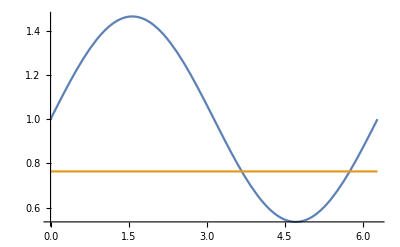

```mathematica
Plot[{α^2+β^2+2α β Sin[x],γ},{x,0,2π}]
```

```mathematica
KroneckerProduct[{{a},{b ⅇ^(ⅈ c)}},{a,b ⅇ^(-ⅈ c)}]//MatrixForm
```

(a^2 | a b ⅇ^(-ⅈ c)
a b ⅇ^(ⅈ c) | b^2)

```mathematica
TrigToExp[Sin[x]]
```

1/2 ⅈ ⅇ^(-ⅈ x)-1/2 ⅈ ⅇ^(ⅈ x)

```mathematica
Solve[{MA==MD, MD==1,...},{α,β,γ},Assumptions->α∈Reals&&β∈Reals&&γ∈Reals&&0<=α<=2π&&0<=β<=2π&&0<=γ<=2π]
```

## general waveplate

```mathematica
QWP = ({{0.5(1-ⅈ)(ⅈ+Cos[2ϕ]), (ⅈ-1)Cos[ϕ]Sin[ϕ]}, {(ⅈ-1)Cos[ϕ]Sin[ϕ], ⅈ Cos[ϕ]^2 Sin[ϕ]^2}});
HWP = ({{Cos[2θ], -2Cos[θ]Sin[θ]}, {-2Cos[θ]Sin[θ], -Cos[2θ]}});
AWP=Exp[-I*eta/2]*{{Cos[theta]^2+Exp[I*eta]*Sin[theta]^2,(1-Exp[I*eta])*Exp[-I*phi]*Cos[theta]*Sin[theta]},{(1-Exp[I*eta])*Exp[I*phi]*Cos[theta]*Sin[theta],Exp[I*eta]*Cos[theta]^2+Sin[theta]^2}};
```

```mathematica
V={1,0};
res =V.(AWP/.{eta->2,phi->4.5,theta->1.9}).(HWP/.θ->ϕ+.1).QWP.V
```

(-1+ⅈ) Cos[ϕ] Sin[ϕ] ((0.503292+0.10853 ⅈ) Cos[2 (0.1+ϕ)]-(1.0806+1.33115 ⅈ) Cos[0.1+ϕ] Sin[ϕ])+(0.5-0.5 ⅈ) (ⅈ+Cos[2 ϕ]) ((0.540302+0.665576 ⅈ) Cos[2 (0.1+ϕ)]+(1.00658+0.217061 ⅈ) Cos[0.1+ϕ] Sin[0.1+ϕ])

```mathematica
Refine[Abs[res]^2//FullSimplify,Assumptions->ϕ ∈Reals]
```

Abs[(0.656199+0.0226428 ⅈ)-(0.022175-0.651696 ⅈ) Cos[2 ϕ]-(0.00450323+0.000467823 ⅈ) Cos[4 ϕ]+(0.291394+0.347549 ⅈ) Cos[ϕ] Sin[ϕ]-(0.029796+0.00309539 ⅈ) Sin[4 ϕ]]^2

```mathematica
a-b Cos[2 ϕ]-c Cos[4 ϕ]+d Cos[ϕ] Sin[ϕ]-f Sin[4 ϕ]
```

```mathematica
π/2
```

```mathematica
Abs[res]^2//FullSimplify
```

ⅇ^Im[eta+2 phi] Abs[ⅇ^(ⅈ phi) Cos[theta]^2 ((0.5-0.5 ⅈ)+(0.5+0.5 ⅈ) Cos[2 ϕ])+ⅇ^(ⅈ (eta+phi)) ((0.5-0.5 ⅈ)+(0.5+0.5 ⅈ) Cos[2 ϕ]) Sin[theta]^2+((-1.-1. ⅈ)+(1.+1. ⅈ) ⅇ^(ⅈ eta)) Cos[theta] Cos[ϕ] Sin[theta] Sin[ϕ]]^2

```mathematica
Refine[Abs[res]^2//FullSimplify,Assumptions->(θ|ϕ|eta|theta|phi)∈Reals]
```

Abs[ⅇ^(ⅈ phi) Cos[theta]^2 ((0.5-0.5 ⅈ)+(0.5+0.5 ⅈ) Cos[2 ϕ])+ⅇ^(ⅈ (eta+phi)) ((0.5-0.5 ⅈ)+(0.5+0.5 ⅈ) Cos[2 ϕ]) Sin[theta]^2+((-1.-1. ⅈ)+(1.+1. ⅈ) ⅇ^(ⅈ eta)) Cos[theta] Cos[ϕ] Sin[theta] Sin[ϕ]]^2

```mathematica
Collect[res,Sin[ϕ]]
```

Abs[(0.5-0.5 ⅈ) (ⅈ+Cos[2 ϕ]) (ⅇ^(-(ⅈ eta)/2) Cos[2 ϕ] (Cos[theta]^2+ⅇ^(ⅈ eta) Sin[theta]^2)-2 ⅇ^(-(ⅈ eta)/2-ⅈ phi) (1-ⅇ^(ⅈ eta)) Cos[theta] Cos[ϕ] Sin[theta] Sin[ϕ])-(1-ⅈ) Cos[ϕ] Sin[ϕ] (-ⅇ^(-(ⅈ eta)/2-ⅈ phi) (1-ⅇ^(ⅈ eta)) Cos[theta] Cos[2 ϕ] Sin[theta]-2 ⅇ^(-(ⅈ eta)/2) Cos[ϕ] (Cos[theta]^2+ⅇ^(ⅈ eta) Sin[theta]^2) Sin[ϕ])]^2

```mathematica
(*period for above is π/2, π for rotating both waveplates together*)
```

```mathematica
Collect[Sin[x]^2+Sin[x]+ⅈ Sin[x],Sin[x]]
```

(1+ⅈ) Sin[x]+Sin[x]^2